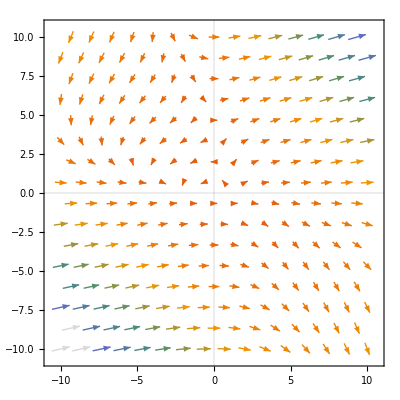

```mathematica
u=(x[t]+y[t])^2-4y[t];
v=x[t]*y[t]+Sin[x[t]];
V=15;
x0=-3;
y0=5;
field=VectorPlot[{(x+y)^2-4y,x*y+Sin[x]},{x,-10,10},{y,-10,10},VectorScaling->Automatic,VectorSizes->Automatic,PlotTheme->"Scientific"]
```

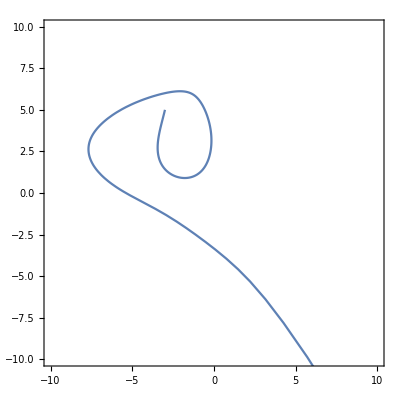

```mathematica
dudx:=D[u,x[t]]
dudy:=D[u,y[t]]
dvdx:=D[v,x[t]]
dvdy:=D[v,y[t]]
eqs={x'[t]==V Cos[β[t]]+u,y'[t]==V Sin[β[t]]+v,β'[t]==dvdx*Sin[β[t]]^2+(dudx-dvdy)*Sin[β[t]]Cos[β[t]]-dudy*Cos[β[t]]^2};
sol=ParametricNDSolve[Join[eqs,{x[0]==x0,y[0]==y0,β[0]==β0}],{x,y,β},{t,0,10},{β0}];

ParametricPlot[Table[{x[β0][t],y[β0][t]}/.sol,{β0,4.5,5.5,0.3}],{t,0,2},Frame->True,PlotRange->{{-10,10},{-10,10}}]
```

{β0→4.95954,tend→0.387522}

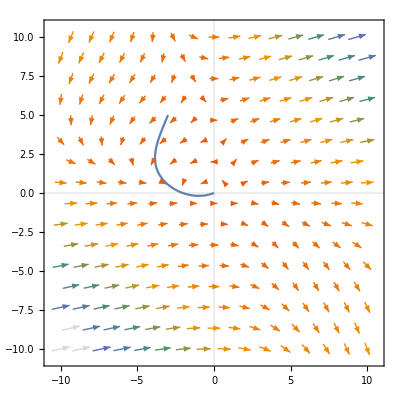

ParametricNDSolve::ndsz: At t == 0.438361, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolve::ndsz: At t == 0.44138, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

```mathematica
koren=FindRoot[{x[β0][tend]==0,y[β0][tend]==0}/.sol,{{β0,4},{tend,0.22}}]
plot =ParametricPlot[{x[β0/.koren][t],y[β0/.koren][t]}/.sol,{t,0,tend/.koren},Frame->True,PlotRange->{{-10,10},{-10,10}}];
Show[field,plot]
```